```mathematica
SetDirectory[NotebookDirectory[]];
dataTc276=Import["Tc_PbPb276_c020.dat"][[2;;]];
dataTu276=Import["Tu_PbPb276_c020.dat"][[2;;]];
dataTs276=Import["Ts_PbPb276_c020.dat"][[2;;]];
dataTc502=Import["Tc_PbPb502_c020.dat"][[2;;]];
dataTu502=Import["Tu_PbPb502_c020.dat"][[2;;]];
dataTs502=Import["Ts_PbPb502_c020.dat"][[2;;]];
```

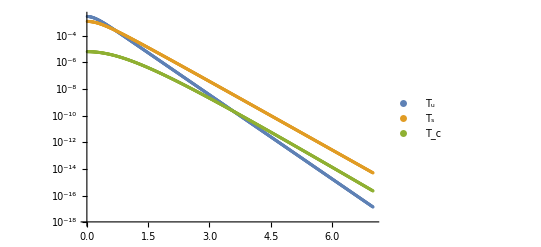

```mathematica
ListLogPlot[{dataTu276,dataTs276,dataTc276},PlotLegends->{"T_u","T_s","T_c"}]
```

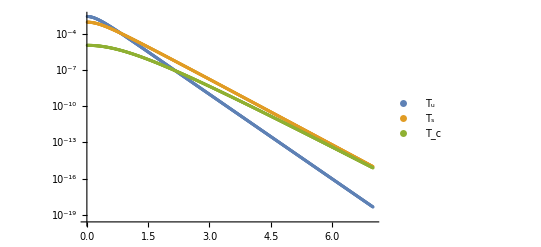

```mathematica
ListLogPlot[{dataTu502,dataTs502,dataTc502},PlotLegends->{"T_u","T_s","T_c"}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
dataTc276=Import["Tc_PbPb276_c020.dat"][[2;;]];
dataTu276=Import["Tu_PbPb276_c020.dat"][[2;;]];
dataTs276=Import["Ts_PbPb276_c020.dat"][[2;;]];
dataTc502=Import["Tc_PbPb502_c020.dat"][[2;;]];
dataTu502=Import["Tu_PbPb502_c020.dat"][[2;;]];
dataTs502=Import["Ts_PbPb502_c020.dat"][[2;;]];
Do[
dataTu276[[i,2]]=Log@dataTu276[[i,2]];
dataTs276[[i,2]]=Log@dataTs276[[i,2]];
dataTc276[[i,2]]=Log@dataTc276[[i,2]];
dataTu502[[i,2]]=Log@dataTu502[[i,2]];
dataTs502[[i,2]]=Log@dataTs502[[i,2]];
dataTc502[[i,2]]=Log@dataTc502[[i,2]];
,{i,1,Length[dataTu276]}]
FindFit[dataTu276,{Log[c]-pt/T,c>0},{{c,10},{T,1}},pt]
FindFit[dataTs276,{Log[c]-pt/T,c>0},{{c,10},{T,1}},pt]
FindFit[dataTc276,{Log[c]-pt/T,c>0},{{c,10},{T,1}},pt]
FindFit[dataTu502,{Log[c]-pt/T,c>0},{{c,10},{T,1}},pt]
FindFit[dataTs502,{Log[c]-pt/T,c>0},{{c,10},{T,1}},pt]
FindFit[dataTc502,{Log[c]-pt/T,c>0},{{c,10},{T,1}},pt]
```

{c→0.00656566,T→0.207605}

{c→0.00364633,T→0.257957}

{c→0.0000645323,T→0.273464}

{c→0.00874643,T→0.18684}

{c→0.00327292,T→0.24423}

{c→0.000110826,T→0.280655}

```mathematica
Tu276[p_]:=0.00656566*Exp[-p/0.20760]
Ts276[p_]:=0.0036463*Exp[-p/0.25795]
Tc276[p_]:=.000064532*Exp[-p/0.27346]
Tu502[p_]:=0.0087464*Exp[-p/0.18684]
Ts502[p_]:=0.0032729*Exp[-p/0.24423]
Tc502[p_]:=0.000110826*Exp[-p/0.280655]
```

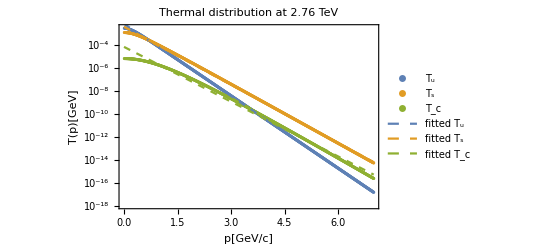

```mathematica
a=Show[ListLogPlot[{dataTu276,dataTs276,dataTc276},PlotLegends->Placed[{Text@Style["T_u",Bold,FontSize->20],Text@Style["T_s",Bold,FontSize->20],Text@Style["T_c",Bold,FontSize->20]},{Right,Top}]],LogPlot[{Tu276[p],Ts276[p],Tc276[p]},{p,0,7},PlotLegends->Placed[{Text@Style["fitted T_u",Bold,FontSize->20],Text@Style["fitted T_s",Bold,FontSize->20],Text@Style["fitted T_c",Bold,FontSize->20]},{Left,Bottom}],PlotStyle->Dashed],Frame->True,PlotLabel->"Thermal distribution at 2.76 TeV",FrameLabel->{"p[GeV/c]","T(p)[GeV]"},
LabelStyle->Directive[Black,Bold,20] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},FrameStyle->Thick]
```

```mathematica
Export["Thermal276.png",Show[a,ImageSize->Large],ImageResolution->500]
```

Thermal276.png

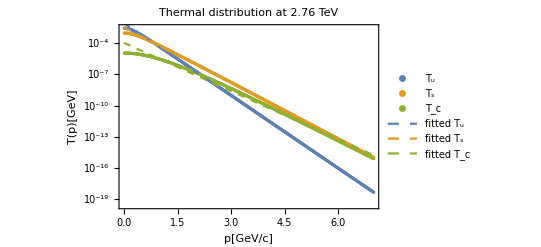

```mathematica
b=Show[ListLogPlot[{dataTu502,dataTs502,dataTc502},PlotLegends->Placed[{Text@Style["T_u",Bold,FontSize->20],Text@Style["T_s",Bold,FontSize->20],Text@Style["T_c",Bold,FontSize->20]},{Right,Top}]],LogPlot[{Tu502[p],Ts502[p],Tc502[p]},{p,0,7},PlotLegends->Placed[{Text@Style["fitted T_u",Bold,FontSize->20],Text@Style["fitted T_s",Bold,FontSize->20],Text@Style["fitted T_c",Bold,FontSize->20]},{Left,Bottom}],PlotStyle->Dashed],Frame->True,PlotLabel->"Thermal distribution at 2.76 TeV",FrameLabel->{"p[GeV/c]","T(p)[GeV]"},
LabelStyle->Directive[Black,Bold,20] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},FrameStyle->Thick]
```

```mathematica
Export["Thermal502.png",Show[b,ImageSize->Large],ImageResolution->500]
```

Thermal502.png